```mathematica
<< Rlink`
```

```mathematica
InstallR[]
```

```mathematica
REvaluate["load(paste(\"~/Rtmp\",\"diamonds.rdata\",sep=\"/\"))"]
```

diamonds

```mathematica
carat =REvaluate["diamonds$carat"];
price = REvaluate["diamonds$price"];
```

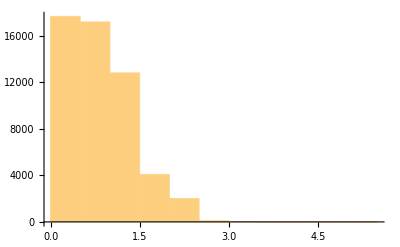

```mathematica
Histogram[carat,{.5}]
```

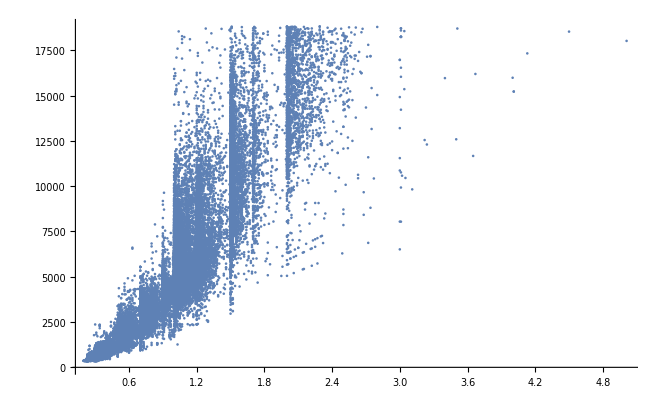

```mathematica
ListPlot[Thread[{carat,price}],PlotRange->Full]
```

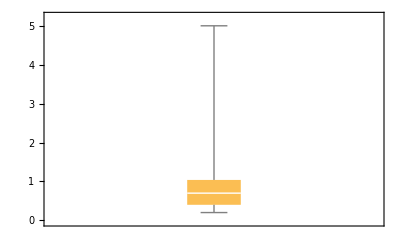

```mathematica
BoxWhiskerChart[carat]
```